```mathematica
IsomorphicGraphQ[Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12}], GraphData["IcosahedralGraph"]]
```

True

```mathematica
GraphSignature2[GraphData["IcosahedralGraph"]]
```

5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
GraphData["IcosahedralGraph"]
```

```mathematica
1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12
1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->7,2<->8,2<->9,2<->3,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->8,8<->13,8<->14,8<->9,9<->14,9<->10,10<->14,10<->11,11<->14,11<->12,12<->14,12<->13,13<->14
1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->7,2<->8,2<->9,2<->3,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->8,8<->13,8<->14,8<->15,8<->9,9<->15,9<->10,10<->15,10<->11,11<->15,11<->14,11<->12,12<->14,12<->13,13<->14,14<->15
```

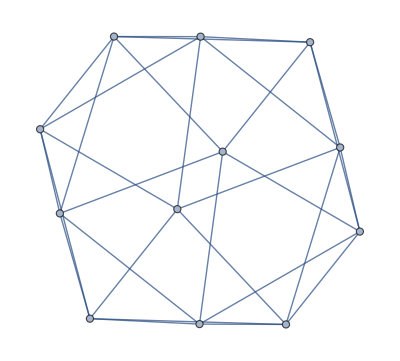

```mathematica
g1=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12}]
```

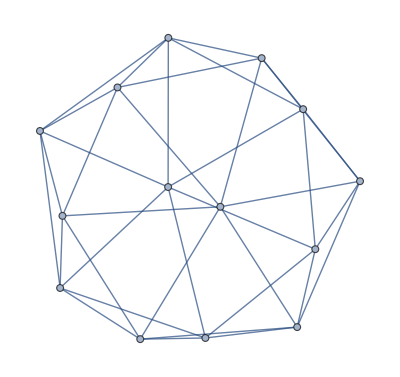

```mathematica
g2=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->7,2<->8,2<->9,2<->3,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->8,8<->13,8<->14,8<->9,9<->14,9<->10,10<->14,10<->11,11<->14,11<->12,12<->14,12<->13,13<->14}]
```

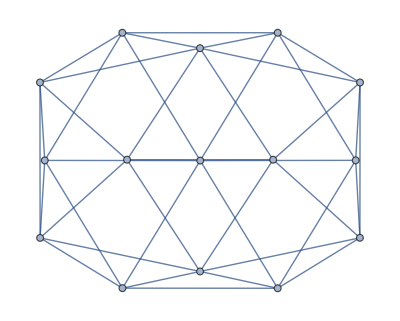

```mathematica
g3=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->7,2<->8,2<->9,2<->3,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->8,8<->13,8<->14,8<->15,8<->9,9<->15,9<->10,10<->15,10<->11,11<->15,11<->14,11<->12,12<->14,12<->13,13<->14,14<->15}]
```

```mathematica
GraphSignature2[g1]
```

5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
GraphSignature2[g2]
```

6-6-5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
GraphSignature2[g3]
```

6-6-6-5-5-5-5-5-5-5-5-5-5-5-5

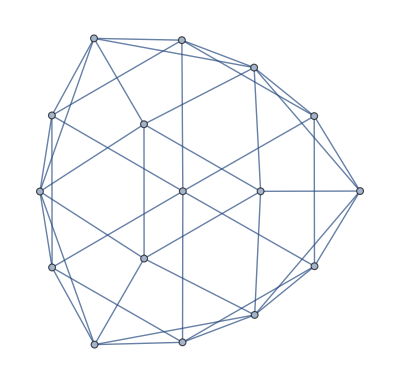

```mathematica
g4=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->14,7<->8,8<->14,8<->9,9<->14,9<->15,9<->10,10<->15,10<->11,11<->15,11<->16,11<->12,12<->16,12<->13,13<->16,13<->14,14<->16,14<->15,15<->16}]
```

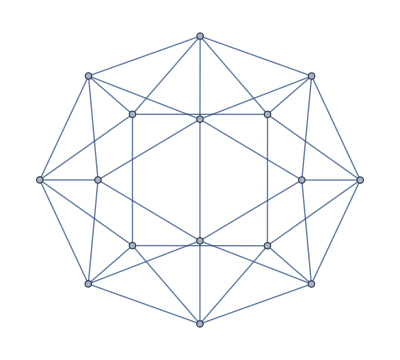

```mathematica
g5=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->7,7<->13,7<->14,7<->8,8<->14,8<->9,9<->14,9<->15,9<->10,10<->15,10<->16,10<->11,11<->16,11<->12,12<->16,12<->13,13<->16,13<->15,13<->14,14<->15,15<->16}]
```

```mathematica
GraphSignature2[g5]
```

6-6-5-5-5-5-5-5-5-5-5-5-5-5-5-5

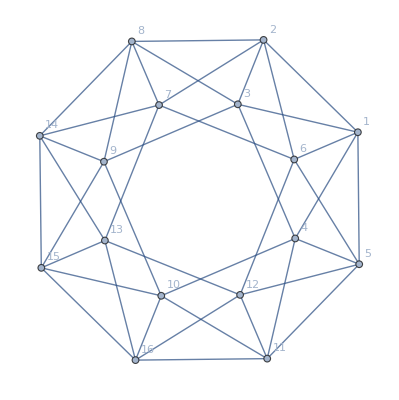

```mathematica
g6=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->7,7<->13,7<->14,7<->8,8<->14,8<->9,9<->14,9<->15,9<->10,10<->15,10<->16,10<->11,11<->16,11<->12,12<->16,12<->13,13<->16,13<->15,13<->14,14<->15,15<->16}, VertexLabels->"Name"]
```

```mathematica
GraphSignature2[g6]
```

5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5

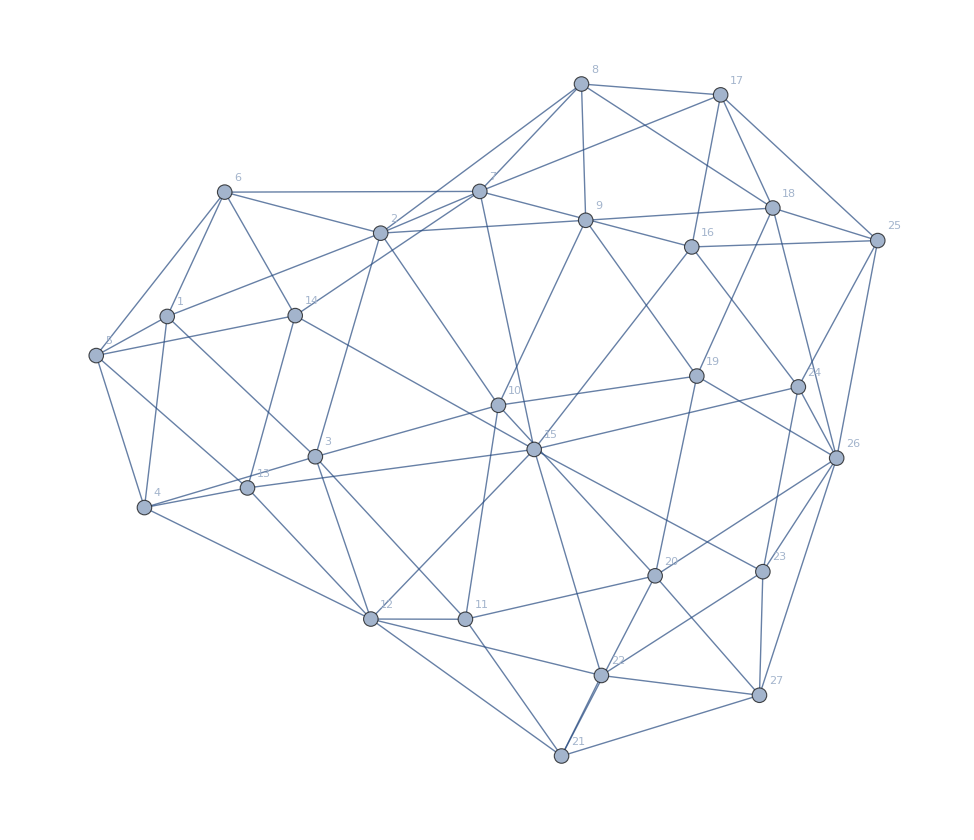

```mathematica
g7=Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->9,2<->10,2<->3,3<->10,3<->11,3<->12,3<->4,4<->12,4<->13,4<->5,5<->13,5<->14,5<->6,6<->14,6<->7,7<->14,7<->15,7<->16,7<->17,7<->8,8<->17,8<->18,8<->9,9<->18,9<->19,9<->10,10<->19,10<->20,10<->11,11<->20,11<->21,11<->12,12<->21,12<->22,12<->15,12<->13,13<->15,13<->14,14<->15,15<->22,15<->23,15<->24,15<->16,16<->24,16<->25,16<->17,17<->25,17<->18,18<->25,18<->26,18<->19,19<->26,19<->20,20<->26,20<->27,20<->21,21<->27,21<->22,22<->27,22<->23,23<->27,23<->26,23<->24,24<->26,24<->25,25<->26,26<->27
}, VertexLabels->"Name"]
```

```mathematica
Select[VertexList[g7],VertexDegree[g7,#]==5&]
```

{1,4,5,6,8,9,11,13,14,16,17,19,21,22,23,24,25,27}

```mathematica
Select[EdgeList[g7],#[[1]]==1||#[[2]]==1&]
```

{1<->2,1<->3,1<->4,1<->5,1<->6}

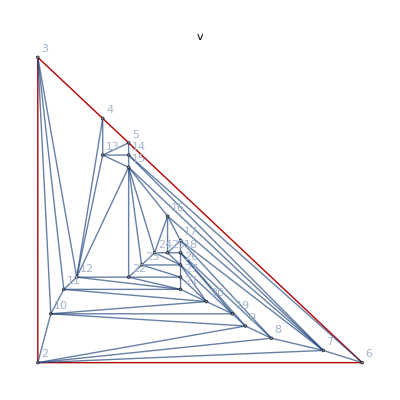

```mathematica
Graph[VertexDelete[g7,1],GraphHighlight->{6<->2,2<->3,3<->4,4<->5,5<->6},PlotLabel->v,GraphLayout->"PlanarEmbedding"]
```

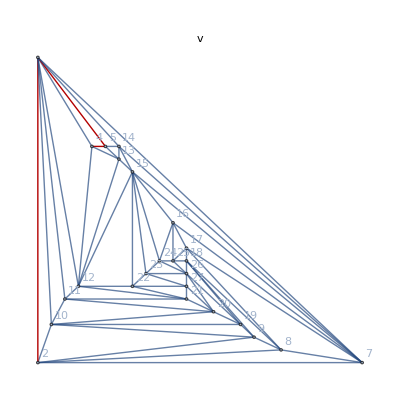

```mathematica
Graph[VertexContract[VertexDelete[g7,1],{6,3}],GraphHighlight->{6<->2,2<->3,3<->4,4<->5,5<->6},PlotLabel->v,GraphLayout->"PlanarEmbedding"]
```

```mathematica
g7
```

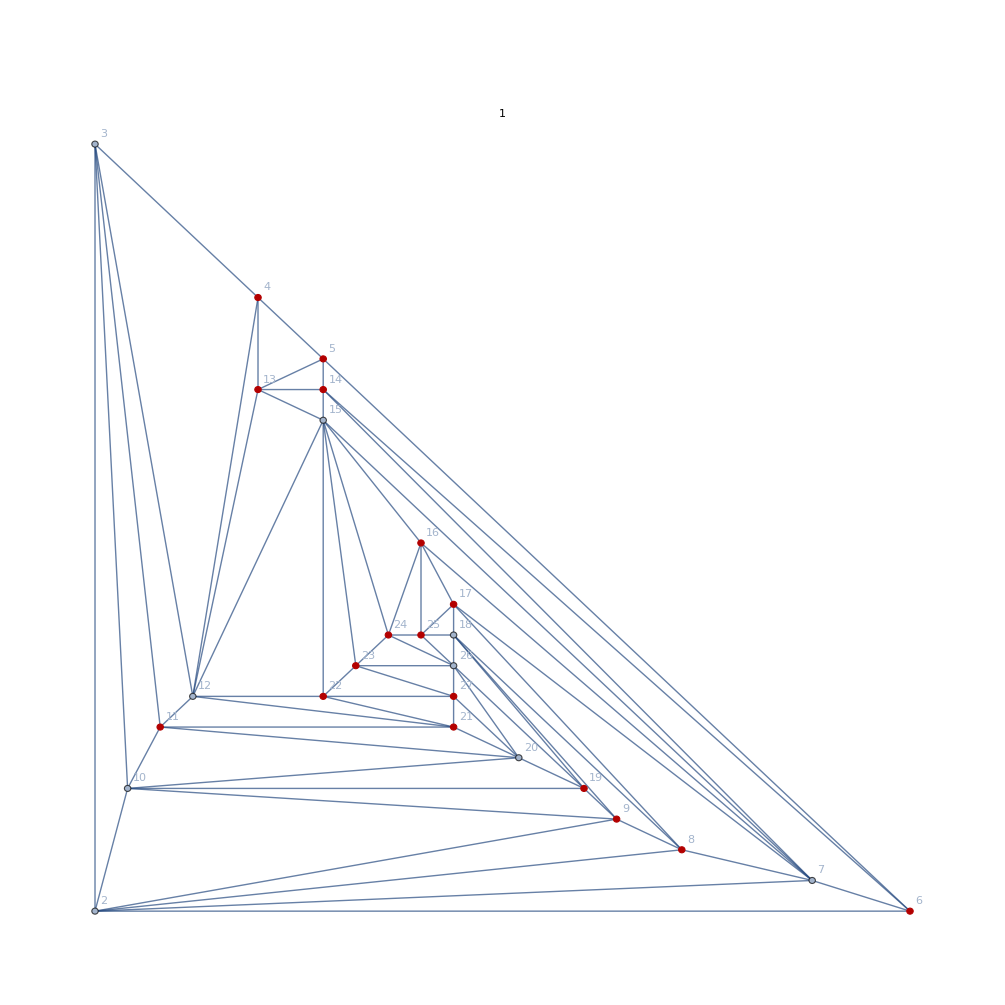
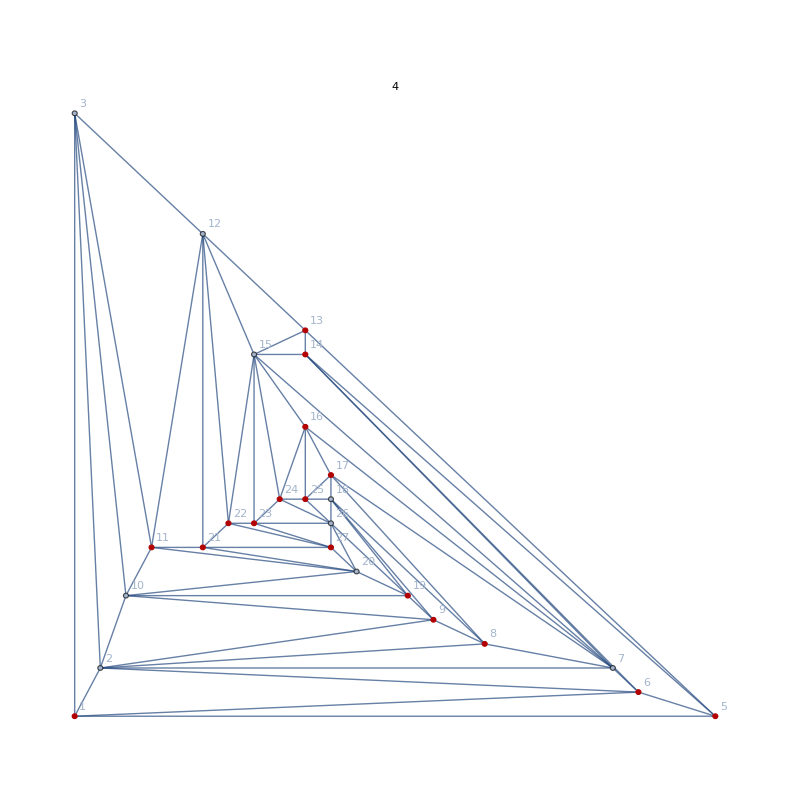
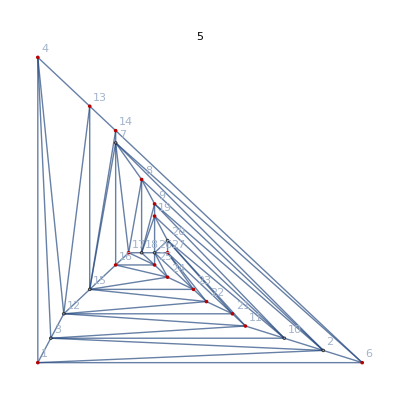
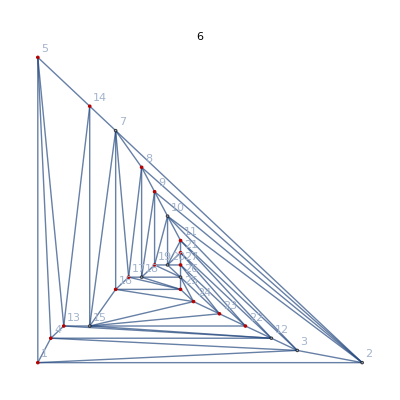
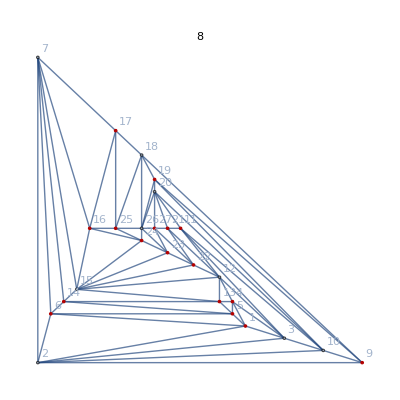
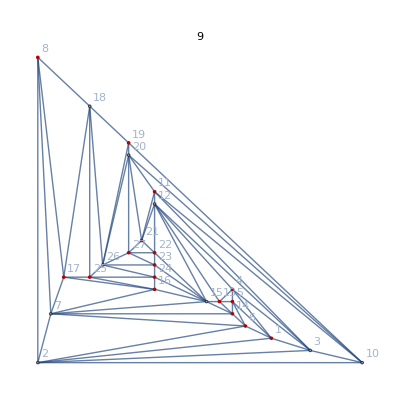
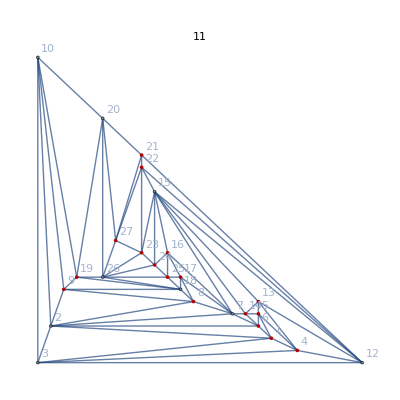
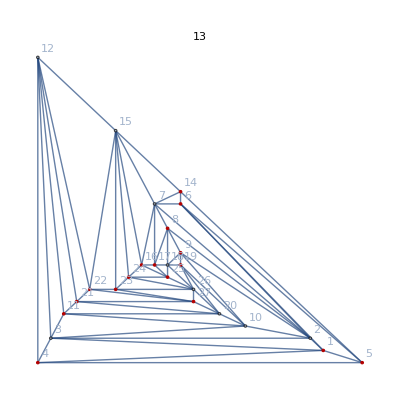

```mathematica
Table[Graph[VertexDelete[g7,v],GraphHighlight->Select[VertexList[g7],VertexDegree[g7,#]==5&],PlotLabel->v,GraphLayout->"PlanarEmbedding"],{v,Select[VertexList[g7],VertexDegree[g7,#]==5&]}]
```

```mathematica
VertexDegree[g7,2]
```

7

```mathematica
GraphSignature2[g7]
```

8-7-7-7-7-6-6-6-6-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->14,7<->8,8<->14,8<->9,9<->14,9<->15,9<->10,10<->15,10<->16,10<->11,11<->16,11<->12,12<->16,12<->13,13<->16,13<->15,13<->14,14<->15,15<->16
```

6-6-5-5-5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
Map[MaximalPlanarQ[#]&,{g1,g2,g3,g4,g5,g6,g7}]
```

{True,True,True,True,False,False,True}